# LSA methods comparison

Anton Antonov
SimplifiedMachineLearningWorkflows-book at GitHub
December 2021

## Setup

## Generate random mandalas data

Generate a (large) list of random mandalas using the function Wolfram Function Repository function RandomMandala evaluated in the Wolfram Kernel through the Python Wolfram Client.

```mathematica
numberOfMandalas=1000;
imageSize=160;
SeedRandom[15];
opts={"Radius"->10,
"RotationalSymmetryOrder"->6,
"ConnectingFunction"->FilledCurve@*BezierCurve,
ImageSize->100};
mandalas=
Table[
ResourceFunction["RandomMandala"]["SymmetricSeed"->RandomChoice[{True,False}],opts],
numberOfMandalas
];
```

Show one of the random mandalas:

```mathematica
mandalas⟦12⟧
```

-Graphics-

Invert the images:

```mathematica
AbsoluteTiming[
mandalas2=ColorNegate[ColorConvert[Image[#,ImageSize->{imageSize,imageSize}],"Grayscale"]]&/@mandalas;
]
```

{86.2381,Null}

Binarize the images:

```mathematica
mandalas3=Binarize/@mandalas2;
```

Show an array of inverted random mandalas:

```mathematica
Multicolumn[RandomSample[mandalas3,100],10]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
(*ResourceFunction["RandomMandala"]["SymmetricSeed"->RandomChoice[{True,False}],"RotationalSymmetryOrder"->3,ImageSize->Large,opts]*)
```

```mathematica
Tally[ImageDimensions/@mandalas3]
```

{{{160,160},1000}}

Convert each image into array and flatten that array:

```mathematica
mandalaArrays=Flatten[ImageData[#]]&/@mandalas3;
Dimensions[mandalaArrays]
```

{1000,25600}

Make a matrix of flattened mandalas:

```mathematica
mandalaMat=SparseArray[N@mandalaArrays]
```

SparseArray[<5664398>, {1000, 25600}]

Make the corresponding SSparseMatrix object:

```mathematica
mandalaSMat=ToSSparseMatrix[mandalaMat,"RowNames"->Automatic,"ColumnNames"->Automatic]
```

SparseArray[<5664398>, {1000, 25600}]

## LSAMon object creation

```mathematica
numberOfTopics=40;
```

Create the LSAMon object:

```mathematica
AbsoluteTiming[
lsaObj=
LSAMonUnit[]⟹
LSAMonSetDocumentTermMatrix[mandalaSMat]⟹
LSAMonApplyTermWeightFunctions["GlobalWeightFunction"->"None","LocalWeightFunction"->"None","NormalizerFunction"->"None"];
]
```

{0.196346,Null}

Here we extract image topics using Singular Value Decomposition (SVD):

```mathematica
AbsoluteTiming[
lsaSVDObj=
lsaObj⟹
LSAMonExtractTopics["NumberOfTopics"->numberOfTopics,Method->"SVD","MaxSteps"->16,"MinNumberOfDocumentsPerTerm"->0];
]
```

{2.63833,Null}

```mathematica
svdH=lsaSVDObj⟹LSAMonNormalizeMatrixProduct[Normalized->Right]⟹LSAMonTakeH
```

SparseArray[<733800>, {40, 25600}]

Here we extract image topics using Non-Negative Matrix Factorization (NNFM):

```mathematica
AbsoluteTiming[
lsaObj=
lsaObj⟹
LSAMonExtractTopics["NumberOfTopics"->numberOfTopics,Method->"NNMF","MaxSteps"->16,"MinNumberOfDocumentsPerTerm"->0];
]
```

{367.858,Null}

```mathematica
nnmfH=lsaObj⟹LSAMonNormalizeMatrixProduct[Normalized->Right]⟹LSAMonTakeH;
```

## Show topics interpretation

### SVD

Show the importance coefficients of the topics (if SVD was used the plot would show the singular values):

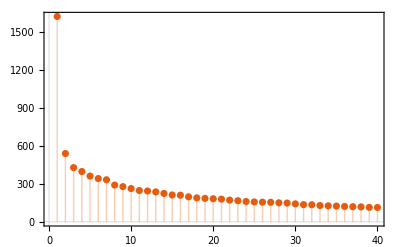

```mathematica
ListPlot[Norm/@SparseArray[lsaSVDObj⟹LSAMonNormalizeMatrixProduct[Normalized->Left]⟹LSAMonTakeH],Filling->Axis,PlotRange->All,PlotTheme->"Scientific"]
```

Show the interpretation of the extracted image topics:

```mathematica
lsaSVDObj⟹
LSAMonNormalizeMatrixProduct[Normalized->Right]⟹LSAMonEchoFunctionContext[ImageAdjust[Image[Partition[#,ImageDimensions[mandalas3⟦1⟧][[1]]]]]&/@SparseArray[#H]&];
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### NNMF

Show the importance coefficients of the topics :

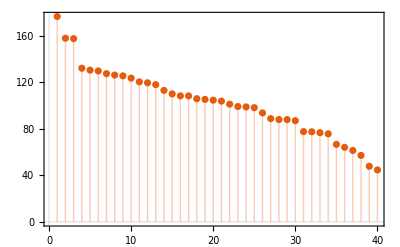

```mathematica
ListPlot[Norm/@SparseArray[lsaObj⟹LSAMonNormalizeMatrixProduct[Normalized->Left]⟹LSAMonTakeH],Filling->Axis,PlotRange->All,PlotTheme->"Scientific"]
```

Show the interpretation of the extracted image topics:

```mathematica
lsaObj⟹
LSAMonNormalizeMatrixProduct[Normalized->Right]⟹LSAMonEchoFunctionContext[ImageAdjust[Image[Partition[#,ImageDimensions[mandalas⟦1⟧][[1]]]]]&/@SparseArray[#H]&];
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Approximation

Get a random mandala from the withheld set:

```mathematica
testMandala=ResourceFunction["RandomMandala"]["SymmetricSeed"->False,"RotationalSymmetryOrder"->6,opts]
```

-Graphics-

```mathematica
testMandala01=Binarize[ColorNegate[ColorConvert[Image[testMandala,ImageSize->{imageSize,imageSize}],"Grayscale"]]]
```

-Graphics-

```mathematica
testMandalaMat=SparseArray[{Flatten[ImageData[testMandala01]]}];
testMandalaSMat=ToSSparseMatrix[testMandalaMat,"RowNames"->Automatic,"ColumnNames"->Automatic]
```

SparseArray[…]

```mathematica
19.5*60
```

1170.

### SVD

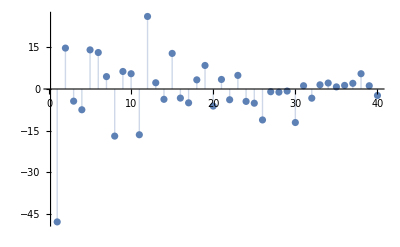

```mathematica
matReprsentation=
lsaSVDObj⟹
LSAMonNormalizeMatrixProduct[Normalized->Right]⟹
LSAMonRepresentByTopics[testMandalaSMat]⟹
LSAMonTakeValue;
lsCoeff=Normal@SparseArray[matReprsentation[[1,All]]];
ListPlot[lsCoeff,Filling->Axis,PlotRange->All]
```

```mathematica
ImageDimensions[testMandala]
```

{100,87}

```mathematica
vecReprsentation=lsCoeff.SparseArray[svdH];
ColorNegate@Image[Rescale[Partition[vecReprsentation,ImageDimensions[testMandala01][[1]]],{0,1}]]
```

-Graphics-

```mathematica
ImageAdjust@%
```

-Graphics-

### NNMF

```mathematica
matReprsentation=
lsaObj⟹
LSAMonRepresentByTopics[testMandalaSMat]⟹
LSAMonTakeValue;
lsCoeff=Normal@SparseArray[matReprsentation[[1,All]]];
ListPlot[lsCoeff,Filling->Axis,PlotRange->All]
```

SparseArray::list: List expected at position 1 in SparseArray[Missing[KeyAbsent,W]].

SparseArray::list: List expected at position 1 in SparseArray[Missing[KeyAbsent,H]].

Set::shape: Lists {MonadicLatentSemanticAnalysis`Private`W,MonadicLatentSemanticAnalysis`Private`H} and RightNormalizeMatrixProduct[SparseArray[Missing[KeyAbsent,W]],SparseArray[Missing[KeyAbsent,H]]] are not the same shape.

SparseArray::list: List expected at position 1 in SparseArray[None].

General::stop: Further output of SparseArray::list will be suppressed during this calculation.

SSparseMatrix::rnset: The row names … are expected to be None, Automatic, or a list of strings with length that equals the number of rows (1) of the SSparseMatrix object.

Part::partd: Part specification $Failed⟦1,All⟧ is longer than depth of object.

SparseArray::list: List expected at position 1 in SparseArray[$Failed⟦1,All⟧].

SparseArray::list: List expected at position 1 in SparseArray[False].

ListPlot::lpn: SparseArray[$Failed⟦1,All⟧] is not a list of numbers or pairs of numbers.

ListPlot[SparseArray[$Failed⟦1,All⟧],Filling→Axis,PlotRange→All]

```mathematica
ImageDimensions[testMandala]
```

{100,87}

```mathematica
vecReprsentation=lsCoeff.SparseArray[nnmfH];
ColorNegate@Image[Rescale[Partition[vecReprsentation,ImageDimensions[testMandala][[1]]],{0,1}]]
```

Image::imgarray: The specified argument Dot[] should be an array of rank 2 or 3 with machine-sized numbers.

ColorNegate::imginv: Image[Dot[]] should be a valid image, a color directive, or a list of such objects.

ColorNegate[Image[Dot[]]]